```mathematica
dataElectronnicComponent={{0,0},{10,167},{20,116},{30,98},{40,76},{50,65},{60,56},{70,44},{80,36},{90,48},{100,64},{110,77},{120,61},{130,46},{140,27},{150,19}}
```

{{0,0},{10,167},{20,116},{30,98},{40,76},{50,65},{60,56},{70,44},{80,36},{90,48},{100,64},{110,77},{120,61},{130,46},{140,27},{150,19}}

```mathematica
TableForm[dataElectronnicComponent,TableHeadings->{None,{"време","брой откази"}}]
```

време | брой откази
0 | 0
10 | 167
20 | 116
30 | 98
40 | 76
50 | 65
60 | 56
70 | 44
80 | 36
90 | 48
100 | 64
110 | 77
120 | 61
130 | 46
140 | 27
150 | 19

```mathematica
kum=Accumulate[dataElectronnicComponent[[All,2]]]
```

{0,167,283,381,457,522,578,622,658,706,770,847,908,954,981,1000}

```mathematica
Table[AppendTo[dataElectronnicComponent[[i]],kum[[i]]],{i,Length[dataElectronnicComponent]}]
```

{{0,0,0},{10,167,167},{20,116,283},{30,98,381},{40,76,457},{50,65,522},{60,56,578},{70,44,622},{80,36,658},{90,48,706},{100,64,770},{110,77,847},{120,61,908},{130,46,954},{140,27,981},{150,19,1000}}

```mathematica
TableForm[dataElectronnicComponent,TableHeadings->{None,{"време","брой откази","кумулативни"}}]
```

време | брой откази | кумулативни
0 | 0 | 0
10 | 167 | 167
20 | 116 | 283
30 | 98 | 381
40 | 76 | 457
50 | 65 | 522
60 | 56 | 578
70 | 44 | 622
80 | 36 | 658
90 | 48 | 706
100 | 64 | 770
110 | 77 | 847
120 | 61 | 908
130 | 46 | 954
140 | 27 | 981
150 | 19 | 1000

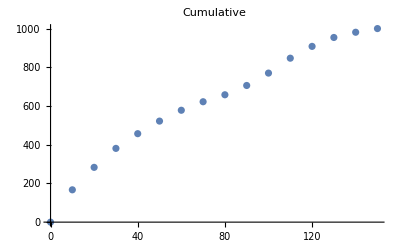

```mathematica
ListPlot[Map[{First[#],Last[#]}&,dataElectronnicComponent],PlotLabel->"Cumulative"]
```

```mathematica
survivors=kum[[-1]]-kum
```

```mathematica
{1000,833,717,619,543,478,422,378,342,294,230,153,92,46,19,0}
Table[AppendTo[dataElectronnicComponent[[i]],survivors[[i]]],{i,Length[dataElectronnicComponent]}]
```

{1000,833,717,619,543,478,422,378,342,294,230,153,92,46,19,0}

{{0,0,0,1000},{10,167,167,833},{20,116,283,717},{30,98,381,619},{40,76,457,543},{50,65,522,478},{60,56,578,422},{70,44,622,378},{80,36,658,342},{90,48,706,294},{100,64,770,230},{110,77,847,153},{120,61,908,92},{130,46,954,46},{140,27,981,19},{150,19,1000,0}}

```mathematica
TableForm[dataElectronnicComponent,TableHeadings->{None,{"време","брой откази","кумулативни","оцелели"}}]
```

време | брой откази | кумулативни | оцелели
0 | 0 | 0 | 1000
10 | 167 | 167 | 833
20 | 116 | 283 | 717
30 | 98 | 381 | 619
40 | 76 | 457 | 543
50 | 65 | 522 | 478
60 | 56 | 578 | 422
70 | 44 | 622 | 378
80 | 36 | 658 | 342
90 | 48 | 706 | 294
100 | 64 | 770 | 230
110 | 77 | 847 | 153
120 | 61 | 908 | 92
130 | 46 | 954 | 46
140 | 27 | 981 | 19
150 | 19 | 1000 | 0

```mathematica
reliability=N[(kum[[-1]]-kum)/kum[[-1]]]
```

{1.,0.833,0.717,0.619,0.543,0.478,0.422,0.378,0.342,0.294,0.23,0.153,0.092,0.046,0.019,0.}

```mathematica
Table[AppendTo[dataElectronnicComponent[[i]],reliability[[i]]],{i,Length[dataElectronnicComponent]}]
```

```mathematica
{{0,0,0,1000,1.},{10,167,167,833,0.833},{20,116,283,717,0.717},{30,98,381,619,0.619},{40,76,457,543,0.543},{50,65,522,478,0.478},{60,56,578,422,0.422},{70,44,622,378,0.378},{80,36,658,342,0.342},{90,48,706,294,0.294},{100,64,770,230,0.23},{110,77,847,153,0.153},{120,61,908,92,0.092},{130,46,954,46,0.046},{140,27,981,19,0.019},{150,19,1000,0,0.}}

TableForm[dataElectronnicComponent,TableHeadings->{None,{"време","брой откази","кумулативни","оцелели","надеждност"}}]
```

{{0,0,0,1000,1.},{10,167,167,833,0.833},{20,116,283,717,0.717},{30,98,381,619,0.619},{40,76,457,543,0.543},{50,65,522,478,0.478},{60,56,578,422,0.422},{70,44,622,378,0.378},{80,36,658,342,0.342},{90,48,706,294,0.294},{100,64,770,230,0.23},{110,77,847,153,0.153},{120,61,908,92,0.092},{130,46,954,46,0.046},{140,27,981,19,0.019},{150,19,1000,0,0.}}

време | брой откази | кумулативни | оцелели | надеждност
0 | 0 | 0 | 1000 | 1.
10 | 167 | 167 | 833 | 0.833
20 | 116 | 283 | 717 | 0.717
30 | 98 | 381 | 619 | 0.619
40 | 76 | 457 | 543 | 0.543
50 | 65 | 522 | 478 | 0.478
60 | 56 | 578 | 422 | 0.422
70 | 44 | 622 | 378 | 0.378
80 | 36 | 658 | 342 | 0.342
90 | 48 | 706 | 294 | 0.294
100 | 64 | 770 | 230 | 0.23
110 | 77 | 847 | 153 | 0.153
120 | 61 | 908 | 92 | 0.092
130 | 46 | 954 | 46 | 0.046
140 | 27 | 981 | 19 | 0.019
150 | 19 | 1000 | 0 | 0.

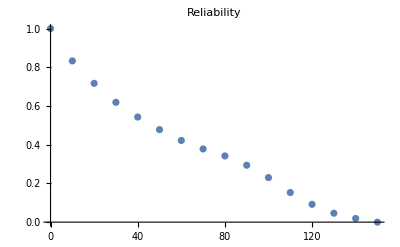

```mathematica
ListPlot[Map[{First[#],Last[#]}&,dataElectronnicComponent],PlotLabel->"Reliability"]
```

```mathematica
kumulativeF =N[kum/kum[[-1]]]
```

```mathematica
{0.,0.167,0.283,0.381,0.457,0.522,0.578,0.622,0.658,0.706,0.77,0.847,0.908,0.954,0.981,1.}
```

```mathematica
Table[AppendTo[dataElectronnicComponent[[i]],kumulativeF[[i]]],{i,Length[dataElectronnicComponent]}]
```

{{0,0,0,1000,1.,0.},{10,167,167,833,0.833,0.167},{20,116,283,717,0.717,0.283},{30,98,381,619,0.619,0.381},{40,76,457,543,0.543,0.457},{50,65,522,478,0.478,0.522},{60,56,578,422,0.422,0.578},{70,44,622,378,0.378,0.622},{80,36,658,342,0.342,0.658},{90,48,706,294,0.294,0.706},{100,64,770,230,0.23,0.77},{110,77,847,153,0.153,0.847},{120,61,908,92,0.092,0.908},{130,46,954,46,0.046,0.954},{140,27,981,19,0.019,0.981},{150,19,1000,0,0.,1.}}

```mathematica
TableForm[dataElectronnicComponent,TableHeadings->{None,{"време","брой откази","кумулативни","оцелели","надеждност","кумулативна вероятност"}}]
```

време | брой откази | кумулативни | оцелели | надеждност | кумулативна вероятност
0 | 0 | 0 | 1000 | 1. | 0.
10 | 167 | 167 | 833 | 0.833 | 0.167
20 | 116 | 283 | 717 | 0.717 | 0.283
30 | 98 | 381 | 619 | 0.619 | 0.381
40 | 76 | 457 | 543 | 0.543 | 0.457
50 | 65 | 522 | 478 | 0.478 | 0.522
60 | 56 | 578 | 422 | 0.422 | 0.578
70 | 44 | 622 | 378 | 0.378 | 0.622
80 | 36 | 658 | 342 | 0.342 | 0.658
90 | 48 | 706 | 294 | 0.294 | 0.706
100 | 64 | 770 | 230 | 0.23 | 0.77
110 | 77 | 847 | 153 | 0.153 | 0.847
120 | 61 | 908 | 92 | 0.092 | 0.908
130 | 46 | 954 | 46 | 0.046 | 0.954
140 | 27 | 981 | 19 | 0.019 | 0.981
150 | 19 | 1000 | 0 | 0. | 1.

```mathematica
dif = Differences[dataElectronnicComponent[[All,1]]]
```

{10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}

```mathematica
density=Append[N[Differences[kum]/(10*1000)],0]
```

{0.0167,0.0116,0.0098,0.0076,0.0065,0.0056,0.0044,0.0036,0.0048,0.0064,0.0077,0.0061,0.0046,0.0027,0.0019,0}

```mathematica
Table[AppendTo[dataElectronnicComponent[[i]],density[[i]]],{i,Length[dataElectronnicComponent]}]
```

{{0,0,0,1000,1.,0.,0.0167},{10,167,167,833,0.833,0.167,0.0116},{20,116,283,717,0.717,0.283,0.0098},{30,98,381,619,0.619,0.381,0.0076},{40,76,457,543,0.543,0.457,0.0065},{50,65,522,478,0.478,0.522,0.0056},{60,56,578,422,0.422,0.578,0.0044},{70,44,622,378,0.378,0.622,0.0036},{80,36,658,342,0.342,0.658,0.0048},{90,48,706,294,0.294,0.706,0.0064},{100,64,770,230,0.23,0.77,0.0077},{110,77,847,153,0.153,0.847,0.0061},{120,61,908,92,0.092,0.908,0.0046},{130,46,954,46,0.046,0.954,0.0027},{140,27,981,19,0.019,0.981,0.0019},{150,19,1000,0,0.,1.,0}}

```mathematica
TableForm[dataElectronnicComponent,TableHeadings->{None,{"време","брой откази","кумулативни","оцелели","надеждност","кумулативна вероятност","плътност"}}]
```

време | брой откази | кумулативни | оцелели | надеждност | кумулативна вероятност | плътност
0 | 0 | 0 | 1000 | 1. | 0. | 0.0167
10 | 167 | 167 | 833 | 0.833 | 0.167 | 0.0116
20 | 116 | 283 | 717 | 0.717 | 0.283 | 0.0098
30 | 98 | 381 | 619 | 0.619 | 0.381 | 0.0076
40 | 76 | 457 | 543 | 0.543 | 0.457 | 0.0065
50 | 65 | 522 | 478 | 0.478 | 0.522 | 0.0056
60 | 56 | 578 | 422 | 0.422 | 0.578 | 0.0044
70 | 44 | 622 | 378 | 0.378 | 0.622 | 0.0036
80 | 36 | 658 | 342 | 0.342 | 0.658 | 0.0048
90 | 48 | 706 | 294 | 0.294 | 0.706 | 0.0064
100 | 64 | 770 | 230 | 0.23 | 0.77 | 0.0077
110 | 77 | 847 | 153 | 0.153 | 0.847 | 0.0061
120 | 61 | 908 | 92 | 0.092 | 0.908 | 0.0046
130 | 46 | 954 | 46 | 0.046 | 0.954 | 0.0027
140 | 27 | 981 | 19 | 0.019 | 0.981 | 0.0019
150 | 19 | 1000 | 0 | 0. | 1. | 0

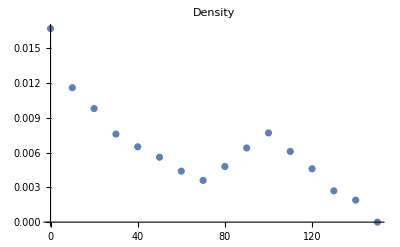

```mathematica
ListPlot[Map[{First[#],Last[#]}&,dataElectronnicComponent],PlotLabel->"Density"]
```

```mathematica
hazard = N[density]/N[reliability]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{0.0167,0.0139256,0.0136681,0.0122779,0.0119705,0.0117155,0.0104265,0.00952381,0.0140351,0.0217687,0.0334783,0.0398693,0.05,0.0586957,0.1,Indeterminate}

```mathematica
density/reliability
```

```mathematica
Table[AppendTo[dataElectronnicComponent[[i]],hazard[[i]]],{i,Length[dataElectronnicComponent]}]
```

{{0,0,0,1000,1.,0.,0.0167,0.0167},{10,167,167,833,0.833,0.167,0.0116,0.0139256},{20,116,283,717,0.717,0.283,0.0098,0.0136681},{30,98,381,619,0.619,0.381,0.0076,0.0122779},{40,76,457,543,0.543,0.457,0.0065,0.0119705},{50,65,522,478,0.478,0.522,0.0056,0.0117155},{60,56,578,422,0.422,0.578,0.0044,0.0104265},{70,44,622,378,0.378,0.622,0.0036,0.00952381},{80,36,658,342,0.342,0.658,0.0048,0.0140351},{90,48,706,294,0.294,0.706,0.0064,0.0217687},{100,64,770,230,0.23,0.77,0.0077,0.0334783},{110,77,847,153,0.153,0.847,0.0061,0.0398693},{120,61,908,92,0.092,0.908,0.0046,0.05},{130,46,954,46,0.046,0.954,0.0027,0.0586957},{140,27,981,19,0.019,0.981,0.0019,0.1},{150,19,1000,0,0.,1.,0,Indeterminate}}

```mathematica
TableForm[dataElectronnicComponent,TableHeadings->{None,{"време","брой откази","кумулативни","оцелели","надеждност","кумулативна вероятност","плътност","интензитет"}}]
```

време | брой откази | кумулативни | оцелели | надеждност | кумулативна вероятност | плътност | интензитет
0 | 0 | 0 | 1000 | 1. | 0. | 0.0167 | 0.0167
10 | 167 | 167 | 833 | 0.833 | 0.167 | 0.0116 | 0.0139256
20 | 116 | 283 | 717 | 0.717 | 0.283 | 0.0098 | 0.0136681
30 | 98 | 381 | 619 | 0.619 | 0.381 | 0.0076 | 0.0122779
40 | 76 | 457 | 543 | 0.543 | 0.457 | 0.0065 | 0.0119705
50 | 65 | 522 | 478 | 0.478 | 0.522 | 0.0056 | 0.0117155
60 | 56 | 578 | 422 | 0.422 | 0.578 | 0.0044 | 0.0104265
70 | 44 | 622 | 378 | 0.378 | 0.622 | 0.0036 | 0.00952381
80 | 36 | 658 | 342 | 0.342 | 0.658 | 0.0048 | 0.0140351
90 | 48 | 706 | 294 | 0.294 | 0.706 | 0.0064 | 0.0217687
100 | 64 | 770 | 230 | 0.23 | 0.77 | 0.0077 | 0.0334783
110 | 77 | 847 | 153 | 0.153 | 0.847 | 0.0061 | 0.0398693
120 | 61 | 908 | 92 | 0.092 | 0.908 | 0.0046 | 0.05
130 | 46 | 954 | 46 | 0.046 | 0.954 | 0.0027 | 0.0586957
140 | 27 | 981 | 19 | 0.019 | 0.981 | 0.0019 | 0.1
150 | 19 | 1000 | 0 | 0. | 1. | 0 | Indeterminate

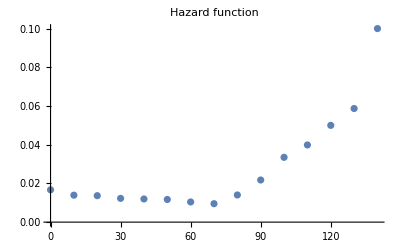

```mathematica
ListPlot[Map[{First[#],Last[#]}&,dataElectronnicComponent],PlotLabel->"Hazard function"]
```